```mathematica
lambda = 515 (*nm*);
NA = 1.3;
```

```mathematica
x[r_]:=2*π*NA*r/lambda
```

```mathematica
I0[P_]:=P*NA^2*π/lambda^2
```

```mathematica
Int[r_,P_]:= I0[P]*(2*BesselJ[1,x[r]]/(x[r]))^2
```

```mathematica
SetDirectory[NotebookDirectory[]];
datalist = Import["2021_09_06-01_46_43-johnson-nv1_2021_09_03.csv", "CSV"]
```

{{0.,0.5,0.4,0.4,0.5,0.4,0.5,0.6,0.5,0.6,0.6,0.3,0.5,0.4,0.4,0.3,0.6,0.5,0.2,0.6,0.4,0.4,0.3,0.3,0.5,0.6,0.2,0.2,0.3,0.1,0.3,0.6,0.1,0.3,0.5,0.6,0.4,0.1,0.4,0.3,0.2,0.3,0.3,0.3,0.2,0.4,0.1,0.4,0.6,0.6,0.2,0.1,0.4,0.,0.6,0.2,0.3,0.5,0.2,0.6,0.,0.1,0.2,0.5,0.2,0.2,0.2,0.2,0.4,0.1,0.3,0.3,0.3,0.2,0.1,0.3,0.5,0.3,0.3,0.3,0.3,0.4,0.,0.7,0.7,0.2,0.2,0.1,0.3,0.3,0.2,0.5,0.2,0.7,0.7,0.8,0.6,0.3,0.6,0.4,0.5,0.4,0.6,0.1,0.2,0.3,0.8,0.5,0.6,0.3,0.3,0.3,0.4,0.3,0.2,0.3,0.6,0.4,0.5,0.6,0.5},119,{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,38,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}
 |  |  |  |

```mathematica
datalist1 = Flatten[datalist];
L = Sqrt[Length[datalist1]]
SPACE=Partition[datalist1,L];
```

121

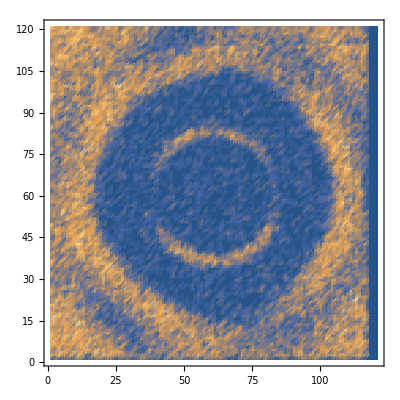

```mathematica
ListDensityPlot[Transpose[SPACE]]
```

```mathematica
gausx= GaussianFilter[Transpose[SPACE],3];
gausxy= GaussianFilter[gausx,3];
```

```mathematica
(*https://reference.wolfram.com/language/guide/ColorSchemes.html*)
```

```mathematica
scale = 20.416666666666725
```

20.4167

```mathematica
Floor[L/2]
```

60

```mathematica
ColorTheme = "DeepSeaColors";(*ColorTheme = "LakeColors";*)
(*ColorTheme = "DeepSeaColors";*)
(*38*)
(*58*)
p1=ListPlot3D[gausxy, DataRange->{{-Floor[L/2],Floor[L/2]},{-Floor[L/2],Floor[L/2]}},Mesh->None, BoundaryStyle->None, RegionFunction->Function[{x,y,z},Sqrt[(x)^2+(y)^2]≤Floor[56]], ColorFunction->ColorTheme, AxesLabel->{"x", "y", "Counts"}];
p2=RevolutionPlot3D[2.5*10^4*Int[r*10,1]+0.065,{r,0,43}, Mesh->None, PlotRange->All,PlotStyle->RGBColor[1,43/255,00, 0.8]];
Show[p1,p2, PlotRange->All]
```

-Graphics3D-

```mathematica
datap1=ListPlot3D[gausxy, DataRange->{{-Floor[L/2],Floor[L/2]},{-Floor[L/2],Floor[L/2]}},Mesh->None, BoundaryStyle->None, RegionFunction->Function[{x,y,z},Sqrt[(x)^2+(y)^2]≤Floor[56]], ColorFunction->ColorTheme,  Axes->False, Boxed->False];
airyp1=RevolutionPlot3D[20*Int[r*10,1]/Int[0.1,1],{r,0,43}, Mesh->None,PlotRange->{Full,Full,{0,0.02}},PlotStyle->RGBColor[1,43/255,00, 0.7],  Axes->False, Boxed->False];Show[datap1,airyp1]
```

-Graphics3D-

```mathematica
Export["airy_n1_combined.png",-Graphics3D-,Background->None,ImageResolution->600]
```

airy_n1_combined.png

```mathematica
r = 7*L/16;datap2=ListPlot3D[gausxy, DataRange->{{-Floor[r],Floor[r]},{-Floor[r],Floor[r]}},Mesh->None, BoundaryStyle->None, RegionFunction->Function[{x,y,z},Sqrt[(x)^2+(y)^2]≤Floor[56]], ColorFunction->ColorTheme,  Axes->False, Boxed->False]
```

-Graphics3D-

```mathematica
Export["n1.png",-Graphics3D-,Background->None,ImageResolution->600]
```

n1.png

```mathematica
airyp2=RevolutionPlot3D[10*Int[r*10,1]/Int[0.1,1],{r,0,80}, Mesh->None,PlotRange->{Full,Full,{0,0.6}},PlotStyle->RGBColor[1,43/255,00, 0.7],BoxRatios->{1,1,1},  Axes->False, Boxed->False,PlotPoints->200,MaxRecursion->10]
```

-Graphics3D-

```mathematica
Export["airy_3.png",-Graphics3D-,Background->None,ImageResolution->600]
```

airy_3.png